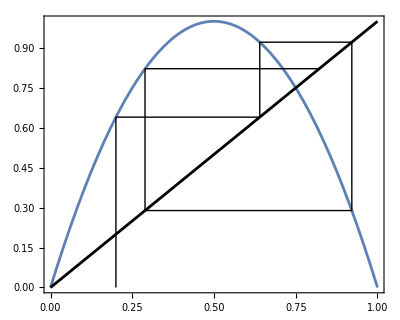

```mathematica
f[x_]:=4x(1-x);
g[{{a_,b_},{c_,d_},{e_,m_}}]:={{e,m},{m,f[m]},{f[m],f[m]}};
range={x,0,1};
n=3;
x0=0.2;
data=NestList[g,{{x0,0},{x0,f[x0]},{f[x0],f[x0]}},n];
Show[Plot[f[x],range],Plot[x,range,PlotStyle->Black],Graphics[Line/@data],AspectRatio->0.8,PlotRange->All,Frame->True]
```